This notebook generates spliced-read performance plots for a given sample. Enter the directory where “.perform” files may be found below. Convert EPSes to PDFs like so: in Mavericks, open in Preview, which automatically converts to PDF. Save. (The proper fonts aren’t embedded by Mathematica’s native PDF exporter.)

```mathematica
SetDirectory["/Users/eterna/Dropbox/performbenpres"];
```

```mathematica
outputDirectory = "/Users/eterna/Dropbox/tempout"
```

/Users/eterna/Dropbox/tempout

```mathematica
(*Select sample*)
```

```mathematica
sampleNames={"NA18508.1.M_111124_1","NA18861.1.M_120209_2"}
```

{NA18508.1.M_111124_1,NA18861.1.M_120209_2}

```mathematica
(*Read pro files for coverage*)
```

```mathematica
TPMs=Table[Import[sampleNames[[i]]~~"_sim.pro"][[All, {6,10}]], {i, 1, 2}];
```

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
(*Compute TPMs*)
```

```mathematica
For[j=1, j≤2, j+=1,For[i=1, i≤2, i+=1,TPMs[[j]][[All, i]] =N[TPMs[[j]][[All, i]] / Total[TPMs[[j]][[All, i]]]]*10^6]];
```

```mathematica
sortedOriginalTPMs=Table[Reverse[Sort[Transpose[TPMs[[i]]][[1]]]], {i, 1, 2}];
```

```mathematica
sortedSimTPMs = Table[Reverse[Sort[Transpose[TPMs[[i]]][[2]]]], {i, 1, 2}];
```

```mathematica
transposedTPMs = Flatten[{Transpose[TPMs[[1]]], Transpose[TPMs[[2]]]},1];
```

```mathematica
hexToRGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&;
```

```mathematica
correlations = Table[Correlation[transposedTPMs[[i]], transposedTPMs[[j]]], {i, 1,4}, {j,1,4}];
```

```mathematica
MatrixForm[correlations]
```

(1. | 0.885803 | 0.828711 | 0.583135
0.885803 | 1. | 0.758476 | 0.726664
0.828711 | 0.758476 | 1. | 0.795256
0.583135 | 0.726664 | 0.795256 | 1.)

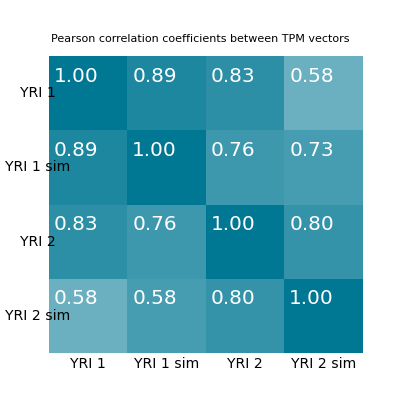

```mathematica
correlationMatrixPlot=Show[MatrixPlot[Table[Correlation[transposedTPMs[[i]], transposedTPMs[[j]]], {i, 1,4}, {j,1,4}], ColorFunction->(Blend[{White,Darker[hexToRGB["#00b3dc"]]},#] &), ColorFunctionScaling->False, Frame->False],
Graphics[Text[Style["1.00", FontFamily->"Palatino", FontSize->20, FontColor->White], {.35,3.73}]],
Graphics[Text[Style["0.89", FontFamily->"Palatino", FontSize->20, FontColor->White], {1.35,3.73}]],
Graphics[Text[Style["0.83", FontFamily->"Palatino", FontSize->20, FontColor->White], {2.35,3.73}]],
Graphics[Text[Style["0.58", FontFamily->"Palatino", FontSize->20, FontColor->White], {3.35,3.73}]],
Graphics[Text[Style["0.76", FontFamily->"Palatino", FontSize->20, FontColor->White], {2.35,2.73}]],
Graphics[Text[Style["1.00", FontFamily->"Palatino", FontSize->20, FontColor->White], {1.35,2.73}]],
Graphics[Text[Style["1.00", FontFamily->"Palatino", FontSize->20, FontColor->White], {2.35,1.73}]],
Graphics[Text[Style["1.00", FontFamily->"Palatino", FontSize->20, FontColor->White], {3.35,0.73}]],
Graphics[Text[Style["0.73", FontFamily->"Palatino", FontSize->20, FontColor->White], {3.35,2.73}]],
Graphics[Text[Style["0.80", FontFamily->"Palatino", FontSize->20, FontColor->White], {2.35,0.73}]],
Graphics[Text[Style["0.80", FontFamily->"Palatino", FontSize->20, FontColor->White], {3.35,1.73}]],
Graphics[Text[Style["0.76", FontFamily->"Palatino", FontSize->20, FontColor->White], {1.35,1.73}]],
Graphics[Text[Style["0.83", FontFamily->"Palatino", FontSize->20, FontColor->White], {0.35,1.73}]],
Graphics[Text[Style["0.89", FontFamily->"Palatino", FontSize->20, FontColor->White], {0.35,2.73}]],
Graphics[Text[Style["0.58", FontFamily->"Palatino", FontSize->20, FontColor->White], {0.35,0.73}]],Graphics[Text[Style["0.58", FontFamily->"Palatino", FontSize->20, FontColor->White], {1.35,0.73}]],
Graphics[Rotate[Text[Style["YRI 1", FontFamily->"Palatino", FontSize->14, FontColor->Black], {-.14,3.5}],90 Degree]],
Graphics[Rotate[Text[Style["YRI 1 sim", FontFamily->"Palatino", FontSize->14, FontColor->Black], {-.14,2.5}],90 Degree]],
Graphics[Rotate[Text[Style["YRI 2", FontFamily->"Palatino", FontSize->14, FontColor->Black], {-.14,1.5}],90 Degree]],
Graphics[Rotate[Text[Style["YRI 2 sim", FontFamily->"Palatino", FontSize->14, FontColor->Black], {-.14,0.5}],90 Degree]],
Graphics[Text[Style["YRI 2 sim", FontFamily->"Palatino", FontSize->14, FontColor->Black], {3.5,-.15}]],
Graphics[Text[Style["YRI 2", FontFamily->"Palatino", FontSize->14, FontColor->Black], {2.5,-.15}]],
Graphics[Text[Style["YRI 1 sim", FontFamily->"Palatino", FontSize->14, FontColor->Black], {1.5,-.15}]],
Graphics[Text[Style["YRI 1", FontFamily->"Palatino", FontSize->14, FontColor->Black], {0.5,-.15}]],
PlotLabel->Style["   Pearson correlation coefficients\n   between TPM vectors", FontFamily->"Trebuchet MS", FontSize->20,
FontColor->Gray]]
```

```mathematica
allTrueStatsFiles=DeleteCases[(If[!StringFreeQ[ #,"true"]&&!StringFreeQ[#,sampleNames[[1]]]&&StringFreeQ[#,"single"]&&(!StringFreeQ[#,"noann"]||!StringFreeQ[#,"rail"]), #]&)/@FileNames["*"],Null]
```

{NA18508.1.M_111124_1.rail.20bioreps.perform_true,NA18508.1.M_111124_1.rail.alone.perform_true,NA18508.1.M_111124_1.star.noann_paired_1pass.perform_true,NA18508.1.M_111124_1.star.noann_paired_2pass.perform_true,NA18508.1.M_111124_1.tophat.noann_paired.perform_true}

```mathematica
allTrueStats = Import[#, "TSV"]&/@allTrueStatsFiles;
```

```mathematica
accumulated=Accumulate/@Transpose/@Transpose/@allTrueStats;
```

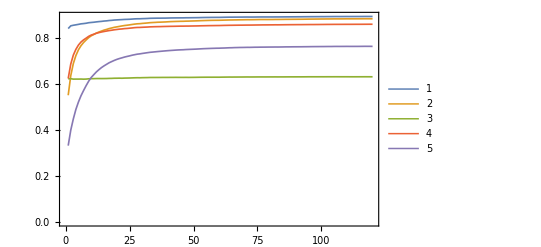

```mathematica
ListPlot[Table[N[#[[4]]]/#[[2]]&/@accumulated[[i]], {i, 1, Length[allTrueStats]}], Joined->True, PlotStyle->Thickness[.003], PlotRange->All, Frame->True,PlotLegends->Automatic, Background->None]
```

```mathematica
Total[allTrueStats[[1]][[All,2]]]
```

3351659

```mathematica
allTrueStats[[1]][[All,2]]
```

{15597,18602,19785,20384,21220,21481,23502,23610,25698,27434,26854,28311,29146,30332,30771,30754,32554,32705,34172,34662,35834,36448,36836,35250,39858,38588,40137,41777,40145,39086,42134,40445,42107,43314,39648,41339,42744,42832,42907,42728,38655,41276,40857,40726,40239,41427,42227,42052,37725,42046,39466,41904,40829,38865,36113,38129,38528,37871,36326,36577,34979,36170,36094,37952,37769,33876,32648,34275,34650,33209,31691,31879,33740,35496,34567,34063,31340,32807,28881,32164,29973,30611,30630,31020,32626,27150,28830,28996,27721,27053,27040,24523,25093,26793,26747,27419,23029,26261,24574,23751}

```mathematica
For[i=1, i≤Length[allTrueStatsFiles], i+= 1,
```

```mathematica
performanceFiles = Select[FileNames["*"], (StringFreeQ[ #,"true"]&)]
```

{corr.pdf,NA18508.1.M_111124_1.rail.perform,NA18508.1.M_111124_1.rail.perform_retrieved,NA18508.1.M_111124_1.rail.perform_summary,NA18508.1.M_111124_1.rail.perform_true,NA18508.1.M_111124_1_sim.pro,NA18508.1.M_111124_1.star.ann_paired_1pass.perform,NA18508.1.M_111124_1.star.ann_paired_1pass.perform_retrieved,NA18508.1.M_111124_1.star.ann_paired_1pass.perform_summary,NA18508.1.M_111124_1.star.ann_paired_1pass.perform_true,NA18508.1.M_111124_1.star.ann_paired_2pass.perform,NA18508.1.M_111124_1.star.ann_paired_2pass.perform_retrieved,NA18508.1.M_111124_1.star.ann_paired_2pass.perform_summary,NA18508.1.M_111124_1.star.ann_paired_2pass.perform_true,NA18508.1.M_111124_1.star.ann_single_1pass.perform,NA18508.1.M_111124_1.star.ann_single_1pass.perform_retrieved,NA18508.1.M_111124_1.star.ann_single_1pass.perform_summary,NA18508.1.M_111124_1.star.ann_single_1pass.perform_true,NA18508.1.M_111124_1.star.ann_single_2pass.perform,NA18508.1.M_111124_1.star.ann_single_2pass.perform_retrieved,NA18508.1.M_111124_1.star.ann_single_2pass.perform_summary,NA18508.1.M_111124_1.star.ann_single_2pass.perform_true,NA18508.1.M_111124_1.star.noann_paired_1pass.perform,NA18508.1.M_111124_1.star.noann_paired_1pass.perform_retrieved,NA18508.1.M_111124_1.star.noann_paired_1pass.perform_summary,NA18508.1.M_111124_1.star.noann_paired_1pass.perform_true,NA18508.1.M_111124_1.star.noann_paired_2pass.perform,NA18508.1.M_111124_1.star.noann_paired_2pass.perform_retrieved,NA18508.1.M_111124_1.star.noann_paired_2pass.perform_summary,NA18508.1.M_111124_1.star.noann_paired_2pass.perform_true,NA18508.1.M_111124_1.star.noann_single_1pass.perform,NA18508.1.M_111124_1.star.noann_single_1pass.perform_retrieved,NA18508.1.M_111124_1.star.noann_single_1pass.perform_summary,NA18508.1.M_111124_1.star.noann_single_1pass.perform_true,NA18508.1.M_111124_1.star.noann_single_2pass.perform,NA18508.1.M_111124_1.star.noann_single_2pass.perform_retrieved,NA18508.1.M_111124_1.star.noann_single_2pass.perform_summary,NA18508.1.M_111124_1.star.noann_single_2pass.perform_true,NA18508.1.M_111124_1.tophat.ann_paired.perform,NA18508.1.M_111124_1.tophat.ann_paired.perform_retrieved,NA18508.1.M_111124_1.tophat.ann_paired.perform_summary,NA18508.1.M_111124_1.tophat.ann_paired.perform_true,NA18508.1.M_111124_1.tophat.ann_single.perform,NA18508.1.M_111124_1.tophat.ann_single.perform_retrieved,NA18508.1.M_111124_1.tophat.ann_single.perform_summary,NA18508.1.M_111124_1.tophat.ann_single.perform_true,NA18508.1.M_111124_1.tophat.noann_paired.perform,NA18508.1.M_111124_1.tophat.noann_paired.perform_retrieved,NA18508.1.M_111124_1.tophat.noann_paired.perform_summary,NA18508.1.M_111124_1.tophat.noann_paired.perform_true,NA18508.1.M_111124_1.tophat.noann_single.perform,NA18508.1.M_111124_1.tophat.noann_single.perform_retrieved,NA18508.1.M_111124_1.tophat.noann_single.perform_summary,NA18508.1.M_111124_1.tophat.noann_single.perform_true,NA18519.1.M_111124_3_sim.pro,NA18858.1.M_120209_7_sim.pro,NA18861.1.M_120209_2.rail.perform,NA18861.1.M_120209_2.rail.perform_retrieved,NA18861.1.M_120209_2.rail.perform_summary,NA18861.1.M_120209_2.rail.perform_true,NA18861.1.M_120209_2_sim.pro,NA18861.1.M_120209_2.star.ann_paired_1pass.perform,NA18861.1.M_120209_2.star.ann_paired_1pass.perform_retrieved,NA18861.1.M_120209_2.star.ann_paired_1pass.perform_summary,NA18861.1.M_120209_2.star.ann_paired_1pass.perform_true,NA18861.1.M_120209_2.star.ann_paired_2pass.perform,NA18861.1.M_120209_2.star.ann_paired_2pass.perform_retrieved,NA18861.1.M_120209_2.star.ann_paired_2pass.perform_summary,NA18861.1.M_120209_2.star.ann_paired_2pass.perform_true,NA18861.1.M_120209_2.star.ann_single_1pass.perform,NA18861.1.M_120209_2.star.ann_single_1pass.perform_retrieved,NA18861.1.M_120209_2.star.ann_single_1pass.perform_summary,NA18861.1.M_120209_2.star.ann_single_1pass.perform_true,NA18861.1.M_120209_2.star.ann_single_2pass.perform,NA18861.1.M_120209_2.star.ann_single_2pass.perform_retrieved,NA18861.1.M_120209_2.star.ann_single_2pass.perform_summary,NA18861.1.M_120209_2.star.ann_single_2pass.perform_true,NA18861.1.M_120209_2.star.noann_paired_1pass.perform,NA18861.1.M_120209_2.star.noann_paired_1pass.perform_retrieved,NA18861.1.M_120209_2.star.noann_paired_1pass.perform_summary,NA18861.1.M_120209_2.star.noann_paired_1pass.perform_true,NA18861.1.M_120209_2.star.noann_paired_2pass.perform,NA18861.1.M_120209_2.star.noann_paired_2pass.perform_retrieved,NA18861.1.M_120209_2.star.noann_paired_2pass.perform_summary,NA18861.1.M_120209_2.star.noann_paired_2pass.perform_true,NA18861.1.M_120209_2.star.noann_single_1pass.perform,NA18861.1.M_120209_2.star.noann_single_1pass.perform_retrieved,NA18861.1.M_120209_2.star.noann_single_1pass.perform_summary,NA18861.1.M_120209_2.star.noann_single_1pass.perform_true,NA18861.1.M_120209_2.star.noann_single_2pass.perform,NA18861.1.M_120209_2.star.noann_single_2pass.perform_retrieved,NA18861.1.M_120209_2.star.noann_single_2pass.perform_summary,NA18861.1.M_120209_2.star.noann_single_2pass.perform_true,NA18861.1.M_120209_2.tophat.ann_paired.perform,NA18861.1.M_120209_2.tophat.ann_paired.perform_retrieved,NA18861.1.M_120209_2.tophat.ann_paired.perform_summary,NA18861.1.M_120209_2.tophat.ann_paired.perform_true,NA18861.1.M_120209_2.tophat.ann_single.perform,NA18861.1.M_120209_2.tophat.ann_single.perform_retrieved,NA18861.1.M_120209_2.tophat.ann_single.perform_summary,NA18861.1.M_120209_2.tophat.ann_single.perform_true,NA18861.1.M_120209_2.tophat.noann_paired.perform,NA18861.1.M_120209_2.tophat.noann_paired.perform_retrieved,NA18861.1.M_120209_2.tophat.noann_paired.perform_summary,NA18861.1.M_120209_2.tophat.noann_paired.perform_true,NA18861.1.M_120209_2.tophat.noann_single.perform,NA18861.1.M_120209_2.tophat.noann_single.perform_retrieved,NA18861.1.M_120209_2.tophat.noann_single.perform_summary,NA18861.1.M_120209_2.tophat.noann_single.perform_true,PCCTPM.pdf}

```mathematica
verboseNameRules = {sampleName~~".rail.perform"->"Rail-RNA", sampleName~~".star.ann_paired_1pass.perform"->"STAR 1-pass paired ann", sampleName~~".star.ann_paired_2pass.perform"->"STAR 2-pass paired ann", sampleName~~".star.noann_paired_1pass.perform"->"STAR 1-pass paired", sampleName~~".star.noann_paired_2pass.perform"->"STAR 2-pass paired",
sampleName~~".star.ann_single_1pass.perform"->"STAR 1-pass single ann", sampleName~~".star.ann_single_2pass.perform"->"STAR 2-pass single ann", sampleName~~".star.noann_single_1pass.perform"->"STAR 1-pass single", sampleName~~".star.noann_single_2pass.perform"->"STAR 2-pass single", sampleName~~".tophat.ann_paired.perform"->"TopHat paired ann", sampleName~~".tophat.ann_single.perform"->"TopHat single ann",
sampleName~~".tophat.noann_paired.perform"->"TopHat paired",
sampleName~~".tophat.noann_single.perform"->"TopHat single"};
```

```mathematica
getPosition[x_]:=Position[performanceFiles,s_String/;StringMatchQ[s,x]][[1,1]]
```

```mathematica
(*parameter varied here is upper bound on lowest true coverage ("true" as in "from simulated alignments") from among introns overlapped by read*)
```

```mathematica
statsAtTrueCoverage[x_, y_] :=Import[StringReplace["!awk '{for (i = 1; i <= threshold; i++){ if ($5 == i) {rel[i] += $1; ret[i] += $2; if ($1 == $2) {relret[i] += $1}}}} END {for (i = 1; i <= threshold; i++) {printf \"%d\\t%d\\t%d\\n\",rel[i],ret[i],relret[i]}}' filename", {"filename"->x,"threshold"->ToString[y]}], "TSV"]
```

```mathematica
statsAboveRetrievedCoverage[x_, y_] :=Import[StringReplace["!awk '{for (i = 1; i <= threshold; i++){ if ($8 >= i) {rel[i] += $1; ret[i] += $2; if ($1 == $2) {relret[i] += $1}}}} END {for (i = 1; i <= threshold; i++) {printf \"%d\\t%d\\t%d\\n\",rel[i],ret[i],relret[i]}}' filename", {"filename"->x,"threshold"->ToString[y]}], "TSV"]
```

```mathematica
(*Up to coverage 100 should be enough to get good plots*)
```

```mathematica
allTrueStats=(statsAtTrueCoverage[#, 100]&)/@performanceFiles;
```

```mathematica
allRetrieved = (statsAboveRetrievedCoverage[#, 100]&)/@performanceFiles;
```

```mathematica
recallPrecisionFromStats[x_] :=
{N[x[[3]] / x[[1]]], N[x[[3]] / x[[2]]]}
```

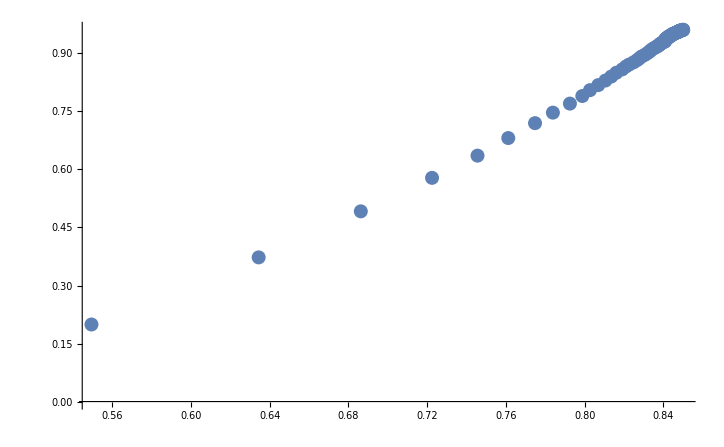

```mathematica
ListPlot[recallPrecisionFromStats/@mystats, PlotRange->All]
```

```mathematica
data = {{10, 20./(7+44/60)}, {20, 20./(5+7/60)}, {40, 20./(3+11/60)}}
```

{{10,2.58621},{20,3.90879},{40,6.28272}}

```mathematica
data = {{10,20./ 9.75609756097561}, {20, 20/7.317073170731708}, {40, 20/4.878048780487805}}
```

{{10,2.05},{20,2.73333},{40,4.1}}

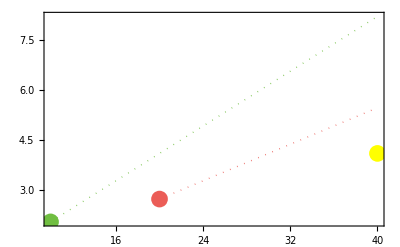

```mathematica
scaling=Show[ListPlot[data, Joined->True,PlotStyle->{White, Thick}], Graphics[{PointSize[.03],RGBColor[112/256,191/256,65/256], Point[data[[1]]]}], Graphics[{PointSize[.03],RGBColor[236/256,93/256,87/256], Point[data[[2]]]}], Graphics[{PointSize[.03],Yellow, Point[data[[3]]]}],
ListPlot[{data[[1]], data[[1]]*2, data[[1]]*4}, Joined->True, PlotStyle->{RGBColor[112/256,191/256,65/256], Dotted, Thickness->0.0025}], 
ListPlot[{data[[2]], data[[2]]*2}, Joined->True, PlotStyle->{RGBColor[236/256,93/256,87/256], Dotted,  Thickness->0.0025}],
(*ParametricPlot[{data[[1]][[1]]x, data[[1]][[2]]Sqrt[x]}, {x, 1, 4}, PlotStyle->{Red, Dotted}],
ParametricPlot[{data[[2]][[1]]x, data[[2]][[2]]Sqrt[x]}, {x, 1, 2}, PlotStyle->{Green, Dotted}],*)
PlotRange->All, Frame->True, FrameStyle->White,ImageSize->Full,BaseStyle->{FontName->"Avenir Next", FontSize->30}, Background->None]
```

```mathematica
c3TwoXLargePricePerHour = 0.525
```

0.525

```mathematica
Ceiling[1/data[[1]][[2]]]*c3TwoXLargePricePerHour*10/20
```

2.1

```mathematica
Ceiling[1/data[[2]][[2]]]*c3TwoXLargePricePerHour*20/20
```

3.15

```mathematica
Ceiling[1/data[[3]][[2]]]*c3TwoXLargePricePerHour*40/20
```

4.2

```mathematica
166./60
```

2.76667

```mathematica
300/60
```

5

```mathematica
546./60
```

9.1

```mathematica
data = {{20, 20/(166/60)}, {40, 40/(300/60)}, {80,80/(546/60)}}
```

{{20,600/83},{40,8},{80,800/91}}

```mathematica
{data[[2]], data[[2]]*2}
```

{{20,1200/307},{40,2400/307}}

```mathematica
{data[[1]], {data[[1]][[1]]*2, data[[2]]}, {data[[1]][[1]]*4, data[[2]]}}
```

{{10,75/29},{20,{20,1200/307}},{40,{20,1200/307}}}

```mathematica
data = {{20, 20/4.878048780487805}, {40, 40/7.317073170731708}, {80,80/12.21835075493612}}
```

{{20,4.1},{40,5.46667},{80,6.54753}}

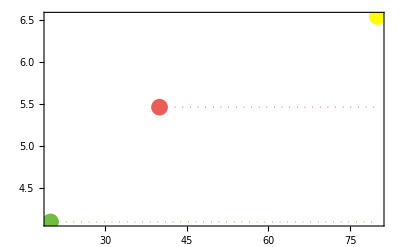

```mathematica
scaling2=Show[ListPlot[data, Joined->True,PlotStyle->{White, Thick}], Graphics[{PointSize[.03],RGBColor[112/256,191/256,65/256], Point[data[[1]]]}], Graphics[{PointSize[.03],RGBColor[236/256,93/256,87/256], Point[data[[2]]]}], Graphics[{PointSize[.03],Yellow, Point[data[[3]]]}],
ListPlot[{data[[1]], {data[[1]][[1]]*2, data[[1]][[2]]}, {data[[1]][[1]]*4, data[[1]][[2]]}}, Joined->True, PlotStyle->{RGBColor[112/256,191/256,65/256], Dotted, Thickness->0.0025}], 
ListPlot[{data[[2]],  {data[[2]][[1]]*2, data[[2]][[2]]}}, Joined->True, PlotStyle->{RGBColor[236/256,93/256,87/256], Dotted,  Thickness->0.0025}],
(*ParametricPlot[{data[[1]][[1]]x, data[[1]][[2]]Sqrt[x]}, {x, 1, 4}, PlotStyle->{Red, Dotted}],
ParametricPlot[{data[[2]][[1]]x, data[[2]][[2]]Sqrt[x]}, {x, 1, 2}, PlotStyle->{Green, Dotted}],*)
PlotRange->All, Frame->True, FrameStyle->White,ImageSize->Full,BaseStyle->{FontName->"Avenir Next", FontSize->30}, Background->None]
```

```mathematica
{data[[1]], data[[1]]*2, data[[1]]*4}
```

{{10,75/29},{20,150/29},{40,300/29}}

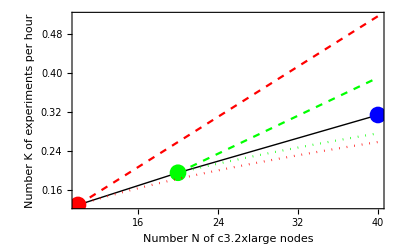

```mathematica
scaling2=Show[ListPlot[data, Joined->True, PlotStyle->{Black, Thick}], Graphics[{PointSize[.03],Red, Point[data[[1]]]}], Graphics[{PointSize[.03],Green, Point[data[[2]]]}], Graphics[{PointSize[.03],Blue, Point[data[[3]]]}],
ListPlot[{data[[1]], data[[1]]*2, data[[1]]*4}, Joined->True, PlotStyle->{Red, Dashed}], 
ListPlot[{data[[2]], data[[2]]*2}, Joined->True, PlotStyle->{Green, Dashed}],
ParametricPlot[{data[[1]][[1]]x, data[[1]][[2]]Sqrt[x]}, {x, 1, 4}, PlotStyle->{Red, Dotted}],
ParametricPlot[{data[[2]][[1]]x, data[[2]][[2]]Sqrt[x]}, {x, 1, 2}, PlotStyle->{Green, Dotted}],
PlotRange->All, Frame->True, FrameLabel->{Style["Number N of c3.2xlarge nodes", FontFamily->"Palatino", FontSize->35],Style["Number K of experiments per hour", FontFamily->"Palatino", FontSize->35]}, ImageSize->Full,BaseStyle->{FontSize->Scaled[.018]}]
```